# Rule 90

### Author

Eric W. Weisstein
August 31, 2016

This notebook downloaded from http://mathworld.wolfram.com/notebooks/CellularAutomata/Rule90.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Rule90.html.

©2016 Wolfram Research, Inc. except for portions noted otherwise

### Initialization

```mathematica
rule=90;
```

## Binary

```mathematica
StringJoin@@(ToString/@IntegerDigits[rule,2,8])
```

01011010

## Plot

#### V5

```mathematica
ElementaryCADiagram[rule]
```

⁃Graphics⁃

#### V6

```mathematica
ElementaryCADiagram[rule]
```

-Graphics-

#### V11

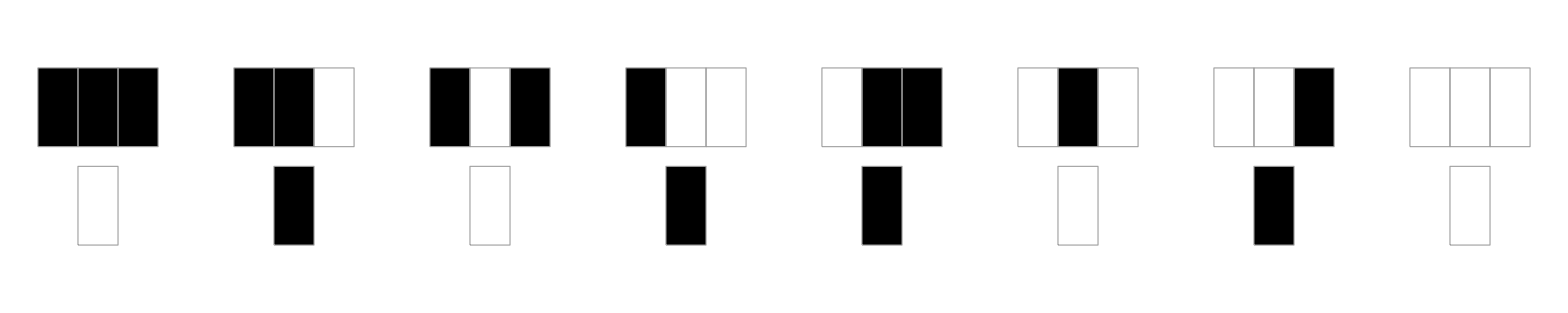

```mathematica
RulePlot[CellularAutomaton[90]]
```

```mathematica
RulePlot[CellularAutomaton[90],{{1},0},15,Mesh->True,PlotLegends->"Icon"]
```

-Graphics-

## Variants

```mathematica
ElementaryCAVariants[rule]
```

{90,165,165}

## Evolution

```mathematica
ArrayPlot[ElementaryCellularAutomaton[rule,250],Frame->False,PixelConstrained->True,ImageSize->1000]
```

⁃Graphics⁃

## Additive Animation

```mathematica
<<GIF`
```

{ByteOrdering:>$ByteOrdering,CharacterEncoding→Automatic,ConversionOptions→{Loop→True,AnimationDisplayTime→0.1},ImageResolution→Automatic,ImageRotated→False,ImageSize→Automatic}

```mathematica
Export[gifs<>"rule"<>ToString[rule]<>".gif",movie=Show/@With[{g=32},
Table[
RasterGraphics[
CellularAutomaton[rule,{
ReplacePart[
Table[0,{2g+1}],1,{{g+1},{s+g+1}}
],0},g,{All,{0,2g+1}}
],
Mesh->False
],
{s,-g,g}]
]]//Timing
```

{15.95 Second,/Volumes/Data/Troves/MathOzTeX/newgifs/rule90.gif}

```mathematica
Show[GraphicsArray[Partition[Take[movie,9],3]]]
```

⁃GraphicsArray⁃

## Triangle of Values

```mathematica
ColumnForm[t=ElementaryCATriangle[rule,7],Center]
```

{1}
{1,0,1}
{1,0,0,0,1}
{1,0,1,0,1,0,1}
{1,0,0,0,0,0,0,0,1}
{1,0,1,0,0,0,0,0,1,0,1}
{1,0,0,0,1,0,0,0,1,0,0,0,1}
{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}

```mathematica
FromDigits/@t
```

{1,101,10001,1010101,100000001,10100000101,1000100010001,101010101010101}

```mathematica
Flatten[t]
```

{1,1,0,1,1,0,0,0,1,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,1,0,1}

### Represented in Decimal

```mathematica
ElementaryCATriangle[rule,20]
```

{{1},{1,0,1},{1,0,0,0,1},{1,0,1,0,1,0,1},{1,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,1,0,1},{1,0,0,0,1,0,0,0,1,0,0,0,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1},{1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1}}

```mathematica
FromDigits[#,2]&/@%
```

{1,5,17,85,257,1285,4369,21845,65537,327685,1114129,5570645,16843009,84215045,286331153,1431655765,4294967297,21474836485,73014444049,365072220245,1103806595329}

```mathematica
FindSequenceFunction[%,n]
```

FindSequenceFunction[{1,5,17,85,257,1285,4369,21845,65537,327685,1114129,5570645,16843009,84215045,286331153,1431655765,4294967297,21474836485,73014444049,365072220245,1103806595329},n]